## Import

```mathematica
img=Import["https://github.com/jschrier/KusamaAnalytics/blob/master/MVIMG_20200307_124815.jpg?raw=true"]
```

-Graphics-

## What’s the coverage level?

```mathematica
DominantColors[img,4,{"Coverage","CoverageImage"},"Dataset"]
```

Dataset[<>]

```mathematica
DominantColors[img,4,"Coverage","ColorAssociation"]
First[#]/Total[#[[1;;2]]]&@%
```

<|RGBColor[0.7820044218454834, 0.12709903181819657, 0.23163927019043712]→0.690174,RGBColor[0.6620464276586641, 0.42457388373504734, 0.012901454793212837]→0.227027,RGBColor[0.0723127402812219, 0.04167477795935259, 0.03785706703449753]→0.0432164,RGBColor[0.5525544281962627, 0.5168820221554004, 0.46387861503694544]→0.0294446|>

0.752478

Conclusion:  75% coverage of the painted surface (excluding frame and background) is filled

## What’s the distribution of circle diameters?

Based on a Helpful blog post:  
https://blog.wolfram.com/2012/01/04/how-to-count-cells-annihilate-sailboats-and-warp-the-mona-lisa/

Comment:  This is complicated by the glare on the top of the image...and the fact that many of the circles touch. So we’ll have to do a little bit of image processing, and will ultimately drop the top 600 rows (of 3100) to get rid of the glare.

```mathematica
pink=First@DominantColors[img,4,"CoverageImage"]
```

-Graphics-

```mathematica
d=DistanceTransform[pink,Padding->0];
marker=MaxDetect[ImageAdjust[d],0.02]
```

-Graphics-

```mathematica
w=WatershedComponents[GradientFilter[pink,3],marker,Method->"Rainfall"];
Colorize[w]
```

-Graphics-

```mathematica
circles=SelectComponents[w,200<#Count<20000&] ;(*selects components that contain this range of pixels*)

Length[circles]
```

3170

```mathematica
measures=ComponentMeasurements[circles,{"Centroid","EquivalentDiskRadius"}];
```

```mathematica
highlightMatches=Show[img,
Graphics[{Blue,Circle@@#&/@measures[[All,2,1;;2]]}]]
```

-Graphics-

Comment:  Note the profusion of blue circles near the top, where we are getting all the glare....we’ll handle this by just cutting out the  top 600 pixels in the image.  The image is 3170 pixels high, so that’s only about 20% of the image, and shouldn’t ruin the statistics.

### Deal with the glare....

```mathematica
ImageTake[highlightMatches,{600,3170}]
```

-Graphics-

```mathematica
ImageDimensions[highlightMatches]
Length[measures] (*how many matches?*)
```

{2569,3170}

2140

```mathematica
belowTheFlare=Select[#[[1,2]]>600&]@Values[measures];
Length[belowTheFlare] (*count of circles after we exclude the top*)
```

1818

```mathematica
%*5/4//N (*rescaling to account for area...actually this is not so bad...*)
```

2272.5

```mathematica
belowTheFlare[[All,1,1]]//MinMax
```

{54.0987,2478.62}

```mathematica
belowTheFlare[[All,1,2]]//MinMax
```

{600.142,3110.79}

## Generate Histograms of the Result

```mathematica
histogramFormat[data_,name_]:=Histogram[
data,
Automatic,"PDF",
Frame->True, FrameLabel->{name,"PDF"}]
```

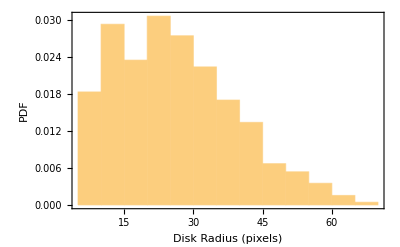

```mathematica
histogramFormat[belowTheFlare[[All,2]],"Disk Radius (pixels)"]
```

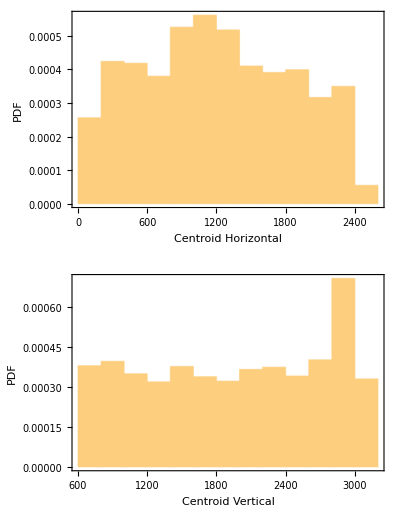

```mathematica
MapThread[
histogramFormat,
{{belowTheFlare[[All,1,1]],belowTheFlare[[All,1,2]]},
{"Centroid Horizontal","Centroid Vertical"}}]//GraphicsColumn
```

Comment:  It appears there is an increased number density towards the bottom of the painting

```mathematica
ImageTake[
highlightMatches,{2750,-1}]
```

-Graphics-

```mathematica
ListPointPlot3D@Partition[#,3]&@Flatten@belowTheFlare
```

-Graphics3D-

Comment:  I tried doing this with “Tweet A Program”, but it doesn’t like pulling image files from Github...

## Where’s the biggest circle?

```mathematica
largest=TakeLargestBy[measures[[All,2,1;;2]],Last,20]
```

{{{2145.01,2311.3},67.3138},{{1444.43,2094.65},67.0982},{{752.068,2969.05},65.8799},{{2109.07,1953.24},65.2633},{{1045.31,438.373},64.0076},{{1773.76,1959.76},63.9254},{{1443.19,2722.67},63.686},{{2269.01,2371.33},63.5935},{{544.22,1501.46},63.5584},{{1839.36,2888.38},63.5283},{{1981.89,3049.46},63.227},{{1860.48,2642.98},62.8584},{{1600.97,714.607},62.6606},{{376.643,656.609},62.5182},{{2409.82,1626.62},60.7886},{{2409.33,1354.15},60.3577},{{2162.41,2020.98},60.1835},{{1797.24,949.547},60.0988},{{2349.64,731.564},60.0511},{{996.285,1626.56},59.7748}}

```mathematica
Show[img,
Graphics[{Blue,(Circle@@#)&/@largest[[1;;2]]}]]
```

-Graphics-